```mathematica
Roots[1/(24  Λ  Ξ^2)  psimax^2 -  l0^2  Λ/(2 Ξ)  psimax + 1/Λ == 0, psimax]
```

psimax==6 (l0^2 Λ^2 Ξ-(√(-2+3 l0^4 Λ^4) Ξ)/(√3))||psimax==6 (l0^2 Λ^2 Ξ+(√(-2+3 l0^4 Λ^4) Ξ)/(√3))

```mathematica
6 l0^2 Λ^2 Ξ-(6 √(-2+3 l0^4 Λ^4) Ξ)/(√3)/.l0->L0 Ξ^(1/2)
```

6 L0^2 Λ^2 Ξ^2-2 √3 Ξ √(-2+3 L0^4 Λ^4 Ξ^2)

```mathematica
Roots[1/Λ-1/2 L0^2 psimax Λ+psimax^2/(24 Λ Ξ^2)+(L0^2 psimax^3 Λ)/(16 Ξ^2)==0,psimax]
```

psimax==-2/(9 L0^2 Λ^2)-(-4-216 L0^4 Λ^4 Ξ^2)/(18 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))+(2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)||psimax==-2/(9 L0^2 Λ^2)+((1+ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1-ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)||psimax==-2/(9 L0^2 Λ^2)+((1-ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1+ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)

```mathematica
Simplify[ComplexExpand[Re[-2/(9 L0^2 Λ^2)+((1+ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1-ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)]],Assumptions->{L0>0,Λ>0,Ξ>0}]
```

Piecewise[{{-(2 (1+√(1+54 L0^4 Λ^4 Ξ^2) Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]+√(3+162 L0^4 Λ^4 Ξ^2) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]))/(9 L0^2 Λ^2), 108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}, {(-2 (1+3078 L0^4 Λ^4 Ξ^2+1303452 L0^8 Λ^8 Ξ^4-157464 L0^12 Λ^12 Ξ^6-54 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)-43740 L0^6 Λ^6 Ξ^3 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^(1/6)-(1+54 L0^4 Λ^4 Ξ^2+(1+3078 L0^4 Λ^4 Ξ^2+1303452 L0^8 Λ^8 Ξ^4-157464 L0^12 Λ^12 Ξ^6-54 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)-43740 L0^6 Λ^6 Ξ^3 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^(1/3)) Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]-√3 (1+54 L0^4 Λ^4 Ξ^2+(1+3078 L0^4 Λ^4 Ξ^2+1303452 L0^8 Λ^8 Ξ^4-157464 L0^12 Λ^12 Ξ^6-54 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)-43740 L0^6 Λ^6 Ξ^3 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^(1/3)) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]])/(9 L0^2 Λ^2 ((1+810 L0^4 Λ^4 Ξ^2-27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^2)^(1/6)), True}}]

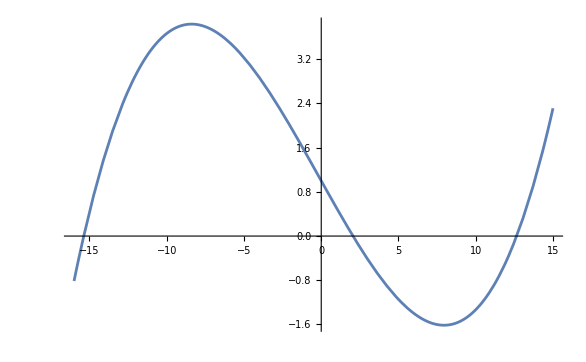

```mathematica
Plot[1-psimax/2+psimax^2/600+psimax^3/400,{psimax,-16,15}]
```

```mathematica
psimaxreal = FullSimplify[1/(9 L0^2 Λ^2)(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]+√3 Sin[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]])),Assumptions->{L0>0,Λ>0,Ξ>0,108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}]
```

(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]+√3 Sin[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]))/(9 L0^2 Λ^2)

```mathematica
Simplify[Series[ psimaxreal,{Ξ,Infinity,4},Assumptions->{L0>0,Λ>0,Ξ>0,108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}]]
```

1/9 (-2/(L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 ⅈ L0^2 Λ^2 Ξ √(-2-888 L0^4 Λ^4 Ξ^2+216 L0^8 Λ^8 Ξ^4)]] (-6 √6 Ξ-1/(3 (√6 L0^4 Λ^4) Ξ)+1/(648 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(18 √2 Ξ+1/(3 √2 L0^4 Λ^4 Ξ)-1/(648 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 ⅈ L0^2 Λ^2 Ξ √(-2-888 L0^4 Λ^4 Ξ^2+216 L0^8 Λ^8 Ξ^4)]])

```mathematica
N[psimaxreal/.{L0->Sqrt[85.7/100],Λ-> 1, Ξ->100}]
```

2.33393

```mathematica
Simplify[1/(9 L0^2 Λ^2)(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(-27 L0^2 Λ^2 Ξ  30 L0^2 Λ^2 Ξ+1)]]+√3 Sin[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(-27 L0^2 Λ^2 Ξ  30 L0^2 Λ^2 Ξ+1)]])),Assumptions-> {L0>0,Λ>0,Ξ>0}]
```

(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]+√3 Sin[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]))/(9 L0^2 Λ^2)

```mathematica
psimax2=(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]+√3 Sin[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]))/(9 L0^2 Λ^2)
```

(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]+√3 Sin[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]))/(9 L0^2 Λ^2)

```mathematica
Series[psimaxreal,{Ξ,Infinity,4},Assumptions->{Ξ>0,Λ>0,L0>0}]
```

-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-2 √(2/3) Ξ-1/(27 (√6 L0^4 Λ^4) Ξ)+1/(5832 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(2 √2 Ξ+1/(27 √2 L0^4 Λ^4 Ξ)-1/(5832 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]

```mathematica
-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-2 √(2/3) Ξ-1/(27 (√6 L0^4 Λ^4) Ξ)+1/(5832 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(2 √2 Ξ+1/(27 √2 L0^4 Λ^4 Ξ)-1/(5832 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]
```

-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-2 √(2/3) Ξ-1/(27 (√6 L0^4 Λ^4) Ξ)+1/(5832 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(2 √2 Ξ+1/(27 √2 L0^4 Λ^4 Ξ)-1/(5832 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]

```mathematica
psimaxE1=-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-(2 (√(2/3) √(L0^4 Λ^4 Ξ^2)) Ξ)/(L0^2 Λ^2 Ξ))+((2 √2 √(L0^4 Λ^4 Ξ^2) Ξ)/(L0^2 Λ^2 Ξ)){{Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]}, {□}};
```

```mathematica
Expand[1/Λ-1/2 L0^2 psimax Λ+psimax^2/(24 Λ Ξ^2)+(L0^2 psimax^3 Λ)/(16 Ξ^2)/. psimax->2/(L0^2 Λ^2)+(4/(3 L0^6 Λ^6))/Ξ^2+(22/(9 L0^10 Λ^10))/Ξ^4]
```

1331/(1458 L0^28 Λ^29 Ξ^14)+121/(81 L0^24 Λ^25 Ξ^12)+803/(243 L0^20 Λ^21 Ξ^10)+232/(81 L0^16 Λ^17 Ξ^8)+161/(54 L0^12 Λ^13 Ξ^6)

```mathematica
Roots[1/Λ-1/2 L0^2 p0 Λ == 0,p0]
```

p0==2/(L0^2 Λ^2)

```mathematica
Roots[2/(3 L0^4 Λ^5 Ξ^2)-(L0^2 p2 Λ)/(2 Ξ^2)==0,p2]
```

p2==4/(3 L0^6 Λ^6)

```mathematica
Roots[11/(9 L0^8 Λ^9 Ξ^4)-(L0^2 p4 Λ)/(2 Ξ^4)==0,p4]
```

p4==22/(9 L0^10 Λ^10)

```mathematica
psimax4=2/(L0^2 Λ^2)+(4/(3 L0^6 Λ^6))/Ξ^2+(22/(9 L0^10 Λ^10))/Ξ^4;
```

```mathematica
sinpsimax4 = Series[Sin[psimax4/2]Cos[psimax4/(2 Ξ)],{Ξ,Infinity,5}]
```

Sin[1/(L0^2 Λ^2)]+((2 Cos[1/(L0^2 Λ^2)])/(3 L0^6 Λ^6)-Sin[1/(L0^2 Λ^2)]/(2 L0^4 Λ^4))/Ξ^2+(64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-16 Sin[1/(L0^2 Λ^2)]-45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^12 Λ^12 Ξ^4)+O[1/Ξ]^6

```mathematica
Solve[Sin[1/(L0^2 Λ^2)]+((2 Cos[1/(L0^2 Λ^2)])/(3 L0^6 Λ^6)-Sin[1/(L0^2 Λ^2)]/(2 L0^4 Λ^4))/Ξ^2+(64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-16 Sin[1/(L0^2 Λ^2)]-45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^12 Λ^12 Ξ^4) == (1-D)/(L0^2 Λ),D]
```

{{D→(72 L0^10 Λ^11 Ξ^4-64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-48 L0^6 Λ^6 Ξ^2 Cos[1/(L0^2 Λ^2)]+16 Sin[1/(L0^2 Λ^2)]+45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)]+36 L0^8 Λ^8 Ξ^2 Sin[1/(L0^2 Λ^2)]-72 L0^12 Λ^12 Ξ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^10 Λ^11 Ξ^4)}}

```mathematica
Series[ (72 L0^10 Λ^11 Ξ^4-64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-48 L0^6 Λ^6 Ξ^2 Cos[1/(L0^2 Λ^2)]+16 Sin[1/(L0^2 Λ^2)]+45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)]+36 L0^8 Λ^8 Ξ^2 Sin[1/(L0^2 Λ^2)]-72 L0^12 Λ^12 Ξ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^10 Λ^11 Ξ^4),{Ξ,Infinity,4}]
```

(1-L0^2 Λ Sin[1/(L0^2 Λ^2)])+(-4 Cos[1/(L0^2 Λ^2)]+3 L0^2 Λ^2 Sin[1/(L0^2 Λ^2)])/(6 L0^4 Λ^5 Ξ^2)+(-64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]+16 Sin[1/(L0^2 Λ^2)]+45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^10 Λ^11 Ξ^4)+O[1/Ξ]^5

```mathematica
Dbif4 = (1-L0^2 Λ Sin[1/(L0^2 Λ^2)])+(-4 Cos[1/(L0^2 Λ^2)]+3 L0^2 Λ^2 Sin[1/(L0^2 Λ^2)])/(6 L0^4 Λ^5 Ξ^2)+(-64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]+16 Sin[1/(L0^2 Λ^2)]+45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^10 Λ^11 Ξ^4);
```

```mathematica
N[Dbif4/.{L0->Sqrt[85.7/100],Λ-> 1.00, Ξ->100}]
```

0.211988

```mathematica
Series[ Cos[psimax4/2]Cos[psimax4/(2Ξ)]/2-Sin[psimax4/2]Sin[psimax4/(2Ξ)]/(2Ξ),{Ξ,Infinity,4}]
```

1/2 Cos[1/(L0^2 Λ^2)]+(-3 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-4 Sin[1/(L0^2 Λ^2)]-6 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(12 L0^6 Λ^6 Ξ^2)+(-16 Cos[1/(L0^2 Λ^2)]-93 L0^4 Λ^4 Cos[1/(L0^2 Λ^2)]-64 L0^2 Λ^2 Sin[1/(L0^2 Λ^2)]-36 L0^6 Λ^6 Sin[1/(L0^2 Λ^2)])/(144 L0^12 Λ^12 Ξ^4)+O[1/Ξ]^5

```mathematica
Dsinpsimax4 = 1/2 Cos[1/(L0^2 Λ^2)]+(-3 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-4 Sin[1/(L0^2 Λ^2)]-6 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(12 L0^6 Λ^6 Ξ^2)+(-16 Cos[1/(L0^2 Λ^2)]-93 L0^4 Λ^4 Cos[1/(L0^2 Λ^2)]-64 L0^2 Λ^2 Sin[1/(L0^2 Λ^2)]-36 L0^6 Λ^6 Sin[1/(L0^2 Λ^2)])/(144 L0^12 Λ^12 Ξ^4)
```

1/2 Cos[1/(L0^2 Λ^2)]+(-3 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-4 Sin[1/(L0^2 Λ^2)]-6 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(12 L0^6 Λ^6 Ξ^2)+(-16 Cos[1/(L0^2 Λ^2)]-93 L0^4 Λ^4 Cos[1/(L0^2 Λ^2)]-64 L0^2 Λ^2 Sin[1/(L0^2 Λ^2)]-36 L0^6 Λ^6 Sin[1/(L0^2 Λ^2)])/(144 L0^12 Λ^12 Ξ^4)

```mathematica
N[Dsinpsimax4 /. {L0->Sqrt[85.7/100],Λ-> 1.00, Ξ->100}]
```

0.196404

```mathematica
energy = Series[Λ + 1/Λ + psimax4/(8 Λ Ξ^2),{Ξ,Infinity,6}]
```

(1/Λ+Λ)+1/(4 L0^2 Λ^3 Ξ^2)+1/(6 L0^6 Λ^7 Ξ^4)+11/(36 L0^10 Λ^11 Ξ^6)+O[1/Ξ]^7

```mathematica
Series[(1/Λ+Λ)+1/(4 L0^2 Λ^3 Ξ^2)+1/(6 L0^6 Λ^7 Ξ^4)+11/(36 L0^10 Λ^11 Ξ^6)/.Λ-> 1+ Λ2/(Ξ^2 )+ Λ4/Ξ^4,{Ξ,Infinity,6}]
```

2+1/(4 L0^2 Ξ^2)+(1/(6 L0^6)-(3 Λ2)/(4 L0^2)+Λ2^2)/Ξ^4+(11/(36 L0^10)-(7 Λ2)/(6 L0^6)-Λ2^3+(24 Λ2^2-12 Λ4)/(16 L0^2)+2 Λ2 Λ4)/Ξ^6+O[1/Ξ]^7

```mathematica
E4 = 2+1/(4 L0^2 Ξ^2)+(1/(6 L0^6)-(3 Λ2)/(4 L0^2)+Λ2^2)/Ξ^4;
```

```mathematica
Solve[D[E4,Λ2]==0,Λ2]
```

{{Λ2→3/(8 L0^2)}}

```mathematica
Λ2->3/(8 L0^2);
```

```mathematica
N[Dbif4/.{L0->Sqrt[8.14/10], Λ-> 1 +  3/(8 8.14/10 10^2),Ξ->10}]
```

0.235197

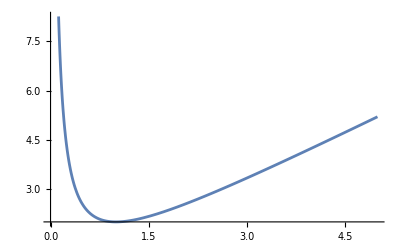

```mathematica
Plot[x+1/x+1/(8 10^2 x ),{x,0,5}]
```

```mathematica
N[psimax4=2/(L0^2 Λ^2)+(4/(3 L0^6 Λ^6))/Ξ^2+(22/(9 L0^10 Λ^10))/Ξ^4/.{L0->Sqrt[85.7/100],Λ-> 1 + 3/(8 85.7/100 100^2), Ξ->100}]
```

2.33373